# Lesson 3 log · The transformer, part by part

Written 2026-11-24 01:51 UTC by lesson3_transformer_parts.nb. 27 of 27 checks pass.

Paper: A. Vaswani et al., Attention Is All You Need, NeurIPS 2017, arXiv:1706.03762. Every part is coded from plain arrays and as a Wolfram net built from primitive layers, and the two are checked against each other. The trained demo net for this paper is in ref3_transformer_vaswani2017.nb; Lesson 4 assembles these parts into a tensor-algebra transformer.

## 1. Scaled dot-product attention

Each query is compared with every key by a dot product; the softmax of the scores gives weights that sum to 1, and the output is the weighted average of the values (Section 3.2.1).

Attention(Q, K, V) = softmax( Q Kᵀ / √dk ) V

PASS  the formula coded from arrays equals AttentionLayer["Dot", "ScoreRescaling" -> "DimensionSqrt"] (4 queries, 7 keys)

PASS  every row of attention weights sums to 1

## 2. Why the scores are divided by √dk

If the components of q and k are independent with mean 0 and variance 1, their dot product has mean 0 and variance dk (footnote 4 of the paper). For dk = 64 the scores are then about ±8, the softmax is close to one-hot, and its gradients are tiny. Dividing by √dk brings the variance back to 1.

| variance of q·k | mean largest softmax weight (10 keys)
unscaled | 63.6 | 0.868
divided by √64 | 0.994 | 0.318

PASS  the variance of q·k is about dk = 64 (measured 63.6)

PASS  after dividing by √dk it is about 1

PASS  unscaled, the softmax is nearly one-hot (largest weight 0.87); scaled it is not (0.32)

## 3. Masks: padding and causal

A mask is added to the scores before the softmax: 0 where attention is allowed, a very large negative number where it is not, so those weights become 0. A padding mask hides the padding at the end of short sequences. A causal mask stops position i of the decoder from seeing positions after i, so that it cannot read the word it is asked to predict (Section 3.2.3).

(0. | −∞ | −∞ | −∞ | −∞
0. | 0. | −∞ | −∞ | −∞
0. | 0. | 0. | −∞ | −∞
0. | 0. | 0. | 0. | −∞
0. | 0. | 0. | 0. | 0.)

PASS  causal: changing positions 5 and 6 leaves outputs 1…4 unchanged

PASS  the causal mask coded from arrays equals AttentionLayer with "Mask" -> "Causal"

PASS  padding: with 4 real keys, changing the 2 padding keys changes nothing

In Wolfram, padding needs no mask: sequences of different lengths are "Varying" dimensions, and NetTrain pads and masks them itself.

## 4. Multi-head attention

One attention with dmodel-dimensional queries is replaced by h attentions with dk = dmodel/h dimensions each, on different learned projections; their outputs are joined and projected again. The total cost is about that of one full-size attention, but each head can attend to different things (Section 3.2.2).

MultiHead(Q, K, V) = Concat(head_1, …, head_h) W^O
head_i = Attention(Q W_i^Q, K W_i^K, V W_i^V)

As a Wolfram net, built from primitive layers: LinearLayer for the projections (all heads at once), ReshapeLayer to split dmodel features into h groups of dk, AttentionLayer with "MultiHead" -> True for the h scaled dot-product attentions, FlattenLayer to join the heads, and a last LinearLayer for W^O.

-Graphics-

PASS  the net built from primitive layers equals multi-head attention coded from arrays (d = 16, h = 4)

PASS  and so does its causal version, used for decoder self-attention

PASS  it has 4(d.b2 + d) = 1088 parameters, whatever the number of heads

## 5. Positional encoding

Attention by itself ignores word order, so a position code is added to each embedding (Section 3.5). Each pair of components is a sine and a cosine of the position, with wavelengths from 2π to 10000·2π.

PE(pos, 2i) = sin(pos / 10000^(2i/dmodel))      PE(pos, 2i+1) = cos(pos / 10000^(2i/dmodel))

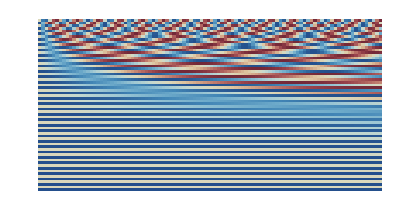

PASS  for every offset k there is one fixed matrix Mₖ (a rotation in each pair of components) with PE(pos + k) = Mₖ PE(pos) for all positions: the reason the paper gives for choosing sinusoids

PASS  the dot product PE(pos)·PE(pos + 7) is the same for every pos: it depends only on the distance

PASS  as a net (SequenceIndicesLayer, a frozen LinearLayer, Sin) it adds exactly these codes, for any length

Frozen means LearningRateMultipliers -> 0: training never changes those weights.

## 6. The position-wise feed-forward network

After attention, every position goes through the same two-layer network on its own: dmodel → dff → dmodel with a ReLU between (dmodel = 512, dff = 2048 in the base model; Section 3.3).

FFN(x) = max(0, x W₁ + b₁) W₂ + b₂

PASS  NetMapOperator[NetChain[{LinearLayer[64], Ramp, LinearLayer[16]}]] equals the formula at every position

## 7. Residual connection and layer normalisation

Each sub-layer (attention or feed-forward) is wrapped in a residual connection and followed by layer normalisation (Section 3.1). The residual lets the signal and its gradient pass straight through; the normalisation keeps every position's vector at mean 0 and variance 1 before a learned scale and shift.

output = LayerNorm(x + Sublayer(x))
LayerNorm(v) = γ (v − mean v)/√(var v + ϵ) + β

PASS  NormalizationLayer[2, 2] is LayerNorm over each position's features, with ϵ = 0.001

The paper places the normalisation after the residual sum (post-norm). Many later transformers place it before the sub-layer (pre-norm), which is easier to train when there are many layers; the lessons follow the paper.

## 8. One encoder layer and one decoder layer

An encoder layer is self-attention, then the feed-forward network, each wrapped as LayerNorm(x + Sublayer(x)). A decoder layer has three sub-layers: causal self-attention over the output so far, attention over the encoder's output (queries from the decoder, keys and values from the encoder), and the feed-forward network. The base model stacks 6 of each (Section 3.1).

-Graphics-

PASS  the encoder layer net equals the encoder layer coded from arrays

PASS  the decoder layer net equals the decoder layer coded from arrays

PASS  the decoder is causal: output i does not change when later output positions change

## 9. Shared embeddings, multiplied by √dmodel

The paper uses one weight matrix for the input embedding, the output embedding and the projection before the softmax, and multiplies the embeddings by √dmodel (Section 3.4). In Wolfram the sharing is NetSharedArray: EmbeddingLayer stores a V×d matrix, and LinearLayer[V] on d-dimensional inputs stores a V×d matrix as well, so one array serves both.

EmbeddingLayer[d, V, "Weights" -> NetSharedArray["W"]]   …   LinearLayer[V, "Weights" -> NetSharedArray["W"]]

PASS  the embedding and the output projection are one and the same array

PASS  the net stores that array once: 160 shared weights and 20 output biases

## 10. Label smoothing

The training target is not one-hot: with ϵ = 0.1 and K classes it puts (1−ϵ) + ϵ/K on the right class and ϵ/K on each of the others. The model learns to be less sure; the paper reports that this hurts perplexity but improves accuracy and BLEU (Section 5.4).

q = (1−ϵ) onehot(y) + ϵ/K ,     loss = −Σ q log p

probability on the right class | 0.999 | 0.955 | 0.91 | 0.82 | 0.55
smoothed loss | 0.83 | 0.519 | 0.5 | 0.533 | 0.814

PASS  the smoothed target sums to 1 and gives 0.91 to the right class

PASS  the smoothed loss is lowest when the model predicts the smoothed target, not when it is 99.9% sure

## 11. The warm-up learning-rate schedule

Adam with β₁ = 0.9, β₂ = 0.98, ϵ = 10⁻⁹. The rate rises linearly for the first 4000 steps, then falls as 1/√step (Section 5.3). The warm-up protects the young network from large, badly-aimed steps.

lrate = dmodel^(−0.5) · min(step^(−0.5), step · warmup^(−1.5)),     warmup = 4000

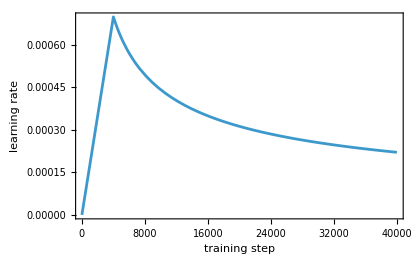

PASS  the peak is at step 4000, at 1/√(512 × 4000) ≈ 7.0×10⁻⁴

In Wolfram: NetTrain[…, Method -> {"ADAM", "Beta1" -> 0.9, "Beta2" -> 0.98, "LearningRate" -> peak, "LearningRateSchedule" -> (atRate[#] / peak &)}]. The schedule is a factor of the learning rate, so the learning rate is set to the peak. (The ADAM ϵ of 10⁻⁹ made training collapse in the demo nets, so they keep Wolfram's default.)

## 12. Beam search with a length penalty

The log-probability of a hypothesis only falls as it grows, so plain beam search prefers short outputs. The paper uses beam size 4 and divides each finished hypothesis's log-probability by a length penalty with α = 0.6 (Section 6.1, from Wu et al. 2016). The beam itself is the one from Lesson 1.

score(Y) = log P(Y | X) / lp(Y),     lp(Y) = ((5 + |Y|) / 6)^α

hypothesis | log P | length | score, α = 0 | score, α = 0.6
short | -2. | 2 | -2. | -1.82
long | -2.6 | 8 | -2.6 | -1.63

PASS  without the penalty the short hypothesis wins; with α = 0.6 the long, slightly less likely one does

## 13. The parameter count of the base model

Counted from the parts above, for dmodel = 512, dff = 2048, h = 8, 6 encoder and 6 decoder layers, and the shared vocabulary of about 37,000 tokens (Section 5.1):

shared embedding / pre-softmax 37000 × 512 | 18,944,000
encoder: 6 × (attention + FFN + 2 LayerNorm) | 18,914,304
decoder: 6 × (2 attentions + FFN + 3 LayerNorm) | 25,224,192
softmax biases | 37,000
total | 63,119,496

PASS  the per-layer formulas agree with Wolfram's counts for small encoder and decoder layers

PASS  the total, 63,119,496, is within 5% of the 65M given in the paper's Table 3; the exact figure depends on the vocabulary and on what is counted

## Where this is used in TensorNets

tnParserNet, tnPolicyNet and tnValueNet are all built from these parts: tnParserNet is a full encoder–decoder, tnPolicyNet and tnValueNet are encoders with small heads on top.

© Computational Classnotes · CC BY-NC-SA 4.0